```mathematica
Needs["VectorFieldPlots`"]
```

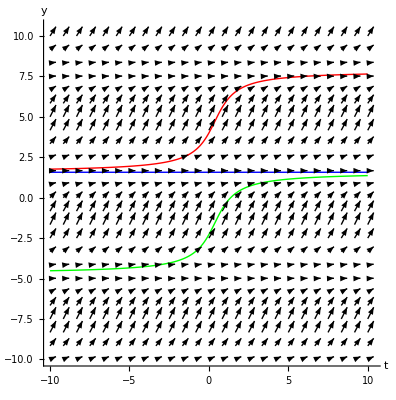

```mathematica
sol1=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==4},y,{t,-10,10}];
plot1=Plot[y[t]/.sol1,{t,-10,10},PlotStyle->{Thick,Red}];
sol2=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==4-2*Pi},y,{t,-10,10}];
plot2=Plot[y[t]/.sol2,{t,-10,10},PlotStyle->{Thick,Green}];
sol3=NDSolve[{y'[t]==1-Sin[y[t]],y[0]==Pi/2},y,{t,-10,10}];
plot3=Plot[y[t]/.sol3,{t,-10,10},PlotStyle->{Thick,Blue}];
Show[dir1,plot1,plot2,plot3,PlotRange->All]
```

```mathematica
dir2 = VectorFieldPlot[{1, y*(y-2)*(y+1)}, {t, 0, 5}, {y, -2, 4}, PlotPoints -> 25, Axes -> True, AxesLabel -> {t, y}]
```

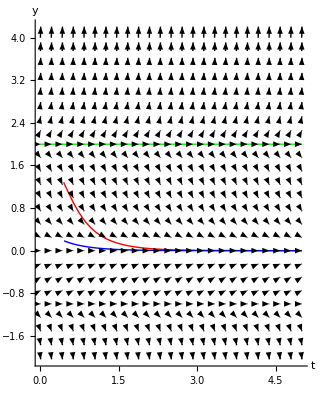

```mathematica
sol3=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==1.9},y,{t,0,5}];
plot3=Plot[y[t]/.sol3,{t,0,5},PlotStyle->{Thick,Red}];
sol4=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==2},y,{t,0,5}];
plot4=Plot[y[t]/.sol4,{t,0,5},PlotStyle->{Thick,Green}];
sol5=NDSolve[{y'[t]==y[t]*(y[t]-2)*(y[t]+1),y[0]==0.5},y,{t,0,5}];
plot5=Plot[y[t]/.sol5,{t,0,5},PlotStyle->{Thick,Blue}];
Show[dir2,plot3,plot4,plot5,PlotRange->All]
```